```mathematica
Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/Std01-m120.wl"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

FileDate::zfname: The file name cannot be an empty string.

Part::partd: Part specification Null⟦3⟧ is longer than depth of object.

Part::partd: Part specification Null⟦2⟧ is longer than depth of object.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FileByteCount::zfname: The file name cannot be an empty string.

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Clear::wrsym: Symbol Discard is Protected.

SetDelayed::write: Tag Discard in Discard[M_,S_] is Protected.

```mathematica
Clear[e,f,F,G,h,M,n,P,p,Q,q,R,s,μ,σ]
```

```mathematica
{M,G} = Get[F="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-speaking-masks/Fig/CorrPlots/P-s/Alle~Sprechen(Sprechen%20mit%20MNS).dat"];
```

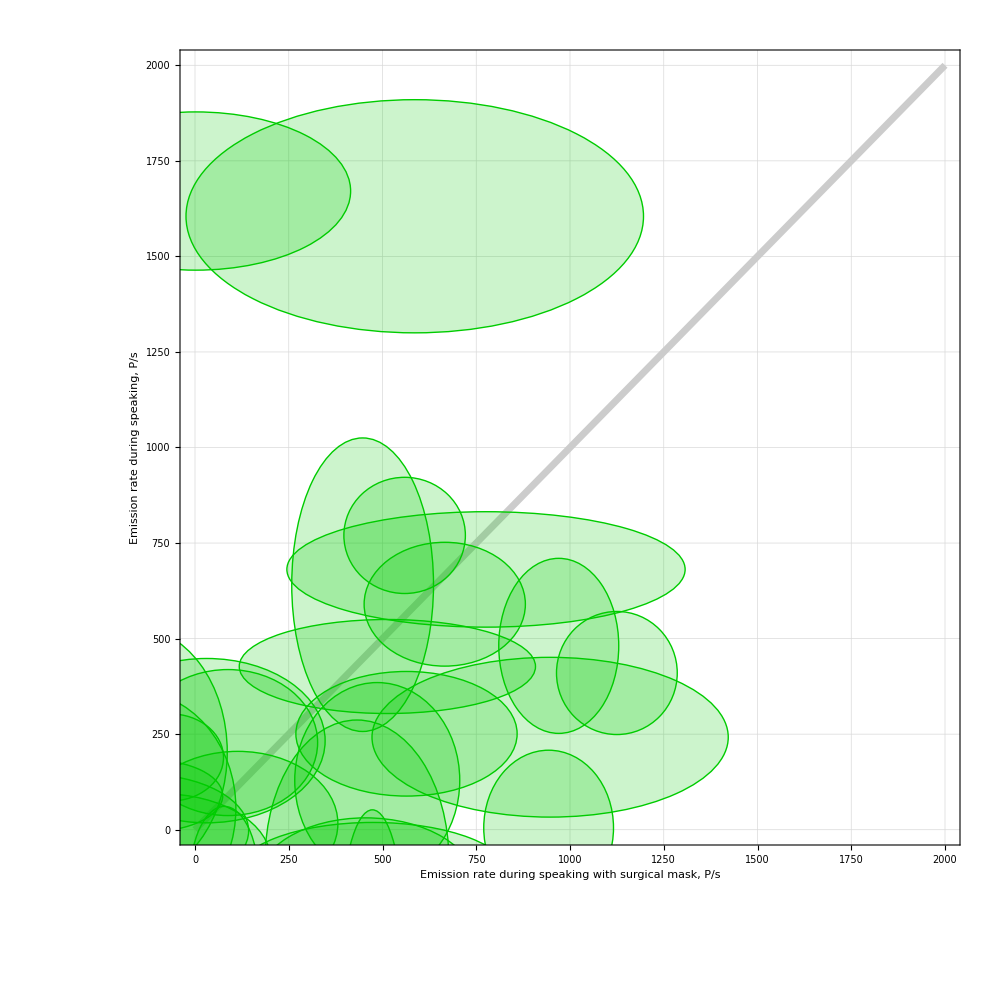

MultinormalDistribution[{2,1671},{{170569,0},{0,42849}}] | P34
MultinormalDistribution[{586,1605},{{372100,0},{0,93025}}] | P43
MultinormalDistribution[{559,770},{{26244,0},{0,23104}}] | P14
MultinormalDistribution[{776,681},{{281961,0},{0,22801}}] | P12
MultinormalDistribution[{447,641},{{35721,0},{0,147456}}] | P2
MultinormalDistribution[{666,590},{{46225,0},{0,26244}}] | P37
MultinormalDistribution[{970,481},{{25600,0},{0,52441}}] | P35
MultinormalDistribution[{513,427},{{156025,0},{0,15129}}] | P11
MultinormalDistribution[{1125,410},{{25921,0},{0,25921}}] | P10
MultinormalDistribution[{564,251},{{87025,0},{0,26569}}] | P5
MultinormalDistribution[{947,242},{{225625,0},{0,43681}}] | P33
MultinormalDistribution[{31,233},{{99856,0},{0,46225}}] | P8
MultinormalDistribution[{88,228},{{57121,0},{0,36481}}] | P6
MultinormalDistribution[{-163,203},{{62001,0},{0,106929}}] | P42
MultinormalDistribution[{-66,189},{{20164,0},{0,12996}}] | P26
MultinormalDistribution[{486,129},{{48400,0},{0,65536}}] | P19
MultinormalDistribution[{-122,89},{{38416,0},{0,8836}}] | P32
MultinormalDistribution[{-164,56},{{74529,0},{0,94249}}] | P25
MultinormalDistribution[{114,16},{{71289,0},{0,35721}}] | P40
MultinormalDistribution[{943,5},{{29929,0},{0,41209}}] | P3
MultinormalDistribution[{-136,-3},{{77841,0},{0,21904}}] | P21
MultinormalDistribution[{432,-79},{{60025,0},{0,133956}}] | P16
MultinormalDistribution[{-89,-80},{{84681,0},{0,30276}}] | P17
MultinormalDistribution[{474,-121},{{135424,0},{0,19600}}] | P20
MultinormalDistribution[{78,-137},{{8649,0},{0,39204}}] | P38
MultinormalDistribution[{455,-144},{{85849,0},{0,30625}}] | P15
MultinormalDistribution[{473,-260},{{6889,0},{0,97344}}] | P41

27

```mathematica
G
TableForm[SortBy[M,-#[[1,1,2]]&]]
Length[M]
```

```mathematica
Mean[LogNormalDistribution[4.908506526878052,1.3066696748075992]]        (*    Sprechen ohne MNS    *)
Mean[LogNormalDistribution[5.629049008402892,0.8450425746478247]]        (*    Sprechen mit  MNS    *)
%/%%
```

318.047

397.859

1.25094

```mathematica
Clear[a,L,Lges]
L = Map[(
h = PDF[#[[1]],{x,y}];
h = h/.(x->a*y);
h = Integrate[h,{y,0,Infinity},Assumptions->{a∈Reals,a>0}];
ReplacePart[#,h,1]
)&,M];
```

```mathematica
i = Length[L];
```

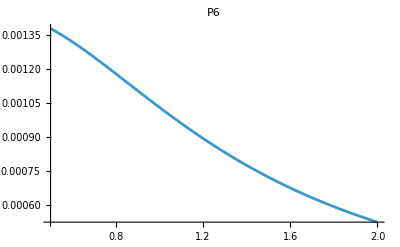

```mathematica
If[i>0,h=L[[i--]];Plot[h[[1]],{a,0.5,2},PlotRange->All,PlotLabel->h[[2]]]]
```

```mathematica
Lges[a_] = Times@@First/@L;
```

```mathematica
FindMaximum[Lges[a],{a,0.9,1.1}]
```

{8.89974×10^-97,{a→1.00945}}

```mathematica
n = 1/First[%]
```

1.12363×10^96

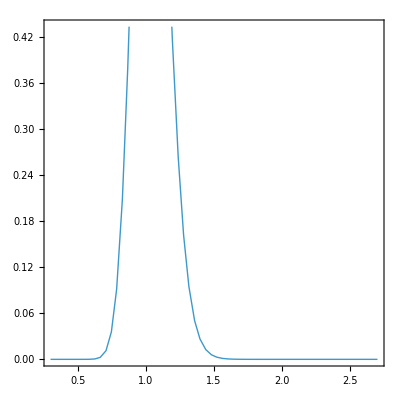

InterpolatingFunction[…]

```mathematica
l = Interpolation[Map[{#,n*Lges[#]}&,Range[0.3,2.7,0.001]]]
```

```mathematica
n= 1/Integrate[l[a],{a,0.3,2.7}]
```

3.27473

```mathematica
f[a_] = n*l[a]
```

-Graphics-

3.27473 InterpolatingFunction[…][a]

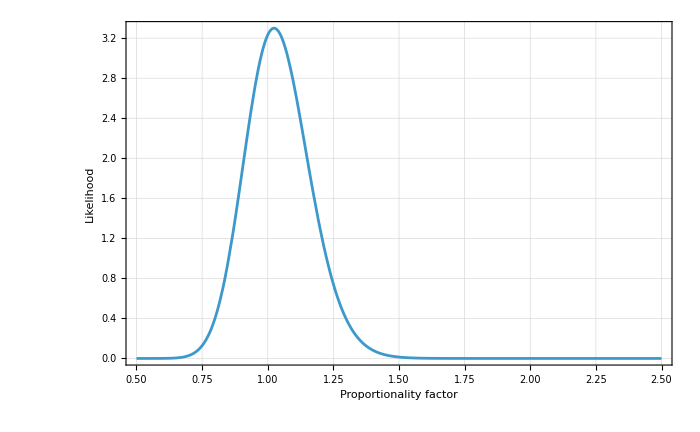

```mathematica
P = Plot[
f[a],{a,0.5,2.5},
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Proportionality factor","Likelihood"},
FrameTicks->{Automatic,None},
GridLines->Automatic,
ImageSize->700,
LabelStyle->{
FontColor->GrayLevel[0],
FontFamily->"Lucida Sans Unicode",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->14},
PlotRange->{All,{0,All}}]
```

```mathematica
NIntegrate[f[x],{x,0.3,2.7}]
```

1.

```mathematica
EV = NIntegrate[x*f[x],{x,0.3,2.7}]                                                   (*    Mean oder Expectation     *)
```

1.04151

```mathematica
Med = q/.FindRoot[NIntegrate[f[x],{x,0.3,q}] ==0.5,{q,1.0}]                     (*    Median     *)
```

NIntegrate::nlim: x = q is not a valid limit of integration.

1.0356

```mathematica
CIlo = q/.FindRoot[NIntegrate[f[x],{x,0.3,q}] ==0.025,{q,0.8}]
```

NIntegrate::nlim: x = q is not a valid limit of integration.

0.817279

```mathematica
CIhi = q/.FindRoot[NIntegrate[f[x],{x,0.3,q}] ==0.975,{q,1.3}]
```

NIntegrate::nlim: x = q is not a valid limit of integration.

1.29949

```mathematica
NIntegrate[f[x],{x,CIlo,CIhi}]
```

0.95

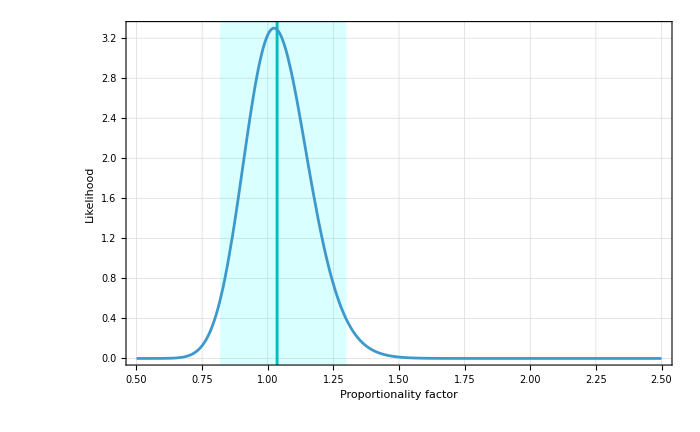

```mathematica
a = 0.6;                                                   (*    Dein neues Farbschema    *)
b = 0.5;

Append[P,Prolog->{
{Hue[1/3,1,0.7],Thickness[0.003],Line[{{Med,-1},{Med,4}}]},
{Hue[1/3,1,1,0.15],Rectangle[{CIlo,-1},{CIhi,4}]}}]/.{
RGBColor[0.368417,0.506779,0.709798]->Hue[a,0.48,0.71],                                                  (*    Kurvenfarbe    *)
Hue[1/3,1,0.7]                                                 ->Hue[b,1,0.7],                                                           (*    Medianlinie    *)
Hue[1/3,1,1,0.15]                                         ->Hue[b,1,1,0.15]                                                      (*    Rechteck       *)
 }
```

```mathematica
Export[NotebookDirectory[]~~"output directory\\Likelihood with outliers.svg",P]
```

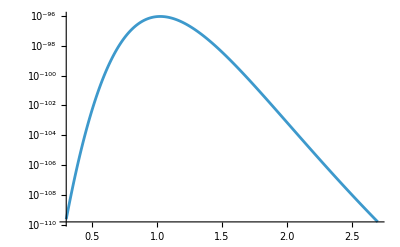

```mathematica
LogPlot[Lges[a],{a,0.3,2.7},PlotPoints->1200]
```

```mathematica
Clear[a,L,Lges,n]
L = Map[(
h = PDF[#[[1]],{x,y}];
h = h/.(x->a*y);
h = Integrate[h,{y,0,Infinity},Assumptions->{a∈Reals,a>0}];
ReplacePart[#,h,1])&,
Select[M,Not[MemberQ[{"P34","P43"},#[[2]]]]&]];
```

```mathematica
i = Length[L];
```

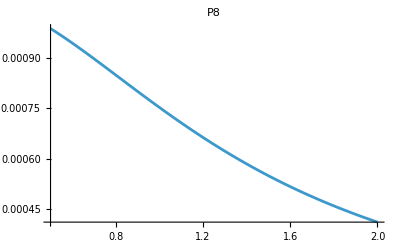

```mathematica
If[i>0,h=L[[i--]];Plot[h[[1]],{a,0.5,2},PlotRange->All,PlotLabel->h[[2]]]]
```

```mathematica
Lges[a_] = Times@@First/@L;
```

```mathematica
FindMaximum[Lges[a],{a,1.3,1.4}]
```

{3.24142×10^-86,{a→1.31827}}

```mathematica
n = 1/First[%]
```

3.08507×10^85

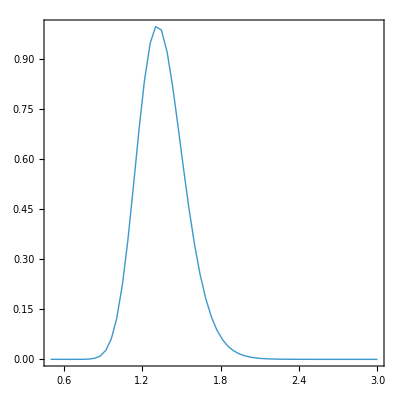

InterpolatingFunction[…]

```mathematica
l = Interpolation[Map[{#,n*Lges[#]}&,Range[0.5,3,0.001]]]
```

```mathematica
n= 1/Integrate[l[a],{a,0.5,3}]
```

2.25923

```mathematica
f[a_] = n*l[a]
```

-Graphics-

2.25923 InterpolatingFunction[…][a]

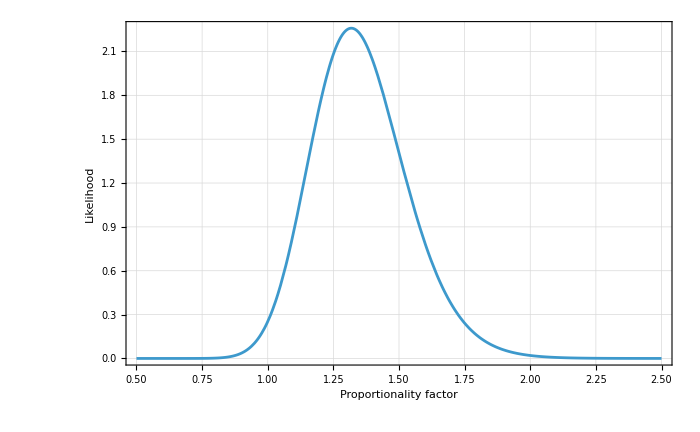

```mathematica
P = Plot[
f[a],{a,0.5,2.5},
DisplayFunction->Identity,
Frame->True,
FrameLabel->{"Proportionality factor","Likelihood"},
FrameTicks->{Automatic,None},
GridLines->Automatic,
ImageSize->700,
LabelStyle->{
FontColor->GrayLevel[0],
FontFamily->"Lucida Sans Unicode",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->14},
PlotRange->{All,{0,All}}]
```

```mathematica
NIntegrate[f[x],{x,0.5,3}]
```

1.

```mathematica
EV = NIntegrate[x*f[x],{x,0.5,3}]                                                   (*    Mean oder Expectation     *)
```

1.35595

```mathematica
Med = q/.FindRoot[NIntegrate[f[x],{x,0.5,q}] ==0.5,{q,1.3}]                     (*    Median     *)
```

NIntegrate::nlim: x = q is not a valid limit of integration.

1.34311

```mathematica
CIlo = q/.FindRoot[NIntegrate[f[x],{x,0.5,q}] ==0.025,{q,1.0}]
```

NIntegrate::nlim: x = q is not a valid limit of integration.

1.03539

```mathematica
CIhi = q/.FindRoot[NIntegrate[f[x],{x,0.5,q}] ==0.975,{q,1.7}]
```

NIntegrate::nlim: x = q is not a valid limit of integration.

1.74997

```mathematica
NIntegrate[f[x],{x,CIlo,CIhi}]
```

0.95

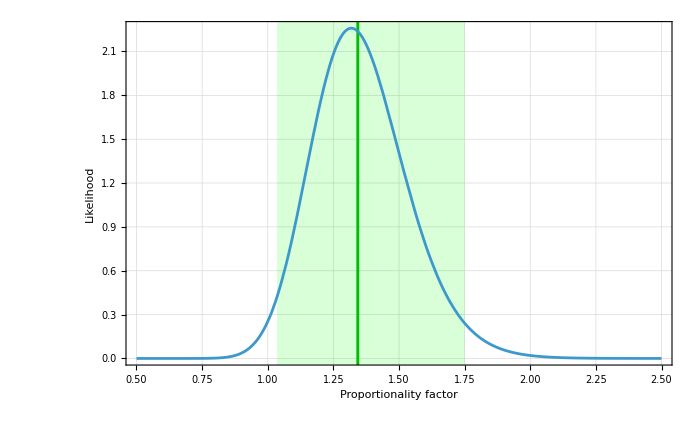

```mathematica
Append[P,Prolog->{
{Hue[1/3,1,0.7],Thickness[0.003],Line[{{Med,-1},{Med,3}}]},
{Hue[1/3,1,1,0.15],Rectangle[{CIlo,-1},{CIhi,3}]}}]
```

```mathematica
Export[NotebookDirectory[]~~"output directory\\Likelihood without outliers.svg",P]
```

```mathematica
S = Range[0.8,2.1,0.01];
S = Map[{#,NIntegrate[f[x],{x,0.5,#}]}&,S]
```

{{0.8,0.0000631153},{0.81,0.0000896438},{0.82,0.000126065},{0.83,0.000175565},{0.84,0.000242183},{0.85,0.000330972},{0.86,0.000448192},{0.87,0.000601515},{0.88,0.000800237},{0.89,0.00105551},{0.9,0.00138056},{0.91,0.00179093},{0.92,0.00230467},{0.93,0.00294253},{0.94,0.00372815},{0.95,0.00468814},{0.96,0.00585215},{0.97,0.00725288},{0.98,0.00892603},{0.99,0.0109101},{1.,0.0132463},{1.01,0.0159779},{1.02,0.0191502},{1.03,0.0228099},{1.04,0.0270045},{1.05,0.0317817},{1.06,0.0371883},{1.07,0.0432704},{1.08,0.0500714},{1.09,0.0576323},{1.1,0.0659901},{1.11,0.0751774},{1.12,0.0852217},{1.13,0.0961444},{1.14,0.107961},{1.15,0.120679},{1.16,0.1343},{1.17,0.148817},{1.18,0.164215},{1.19,0.180473},{1.2,0.19756},{1.21,0.215439},{1.22,0.234067},{1.23,0.253393},{1.24,0.273359},{1.25,0.293904},{1.26,0.314962},{1.27,0.336462},{1.28,0.358332},{1.29,0.380495},{1.3,0.402876},{1.31,0.425397},{1.32,0.447982},{1.33,0.470555},{1.34,0.493043},{1.35,0.515375},{1.36,0.537483},{1.37,0.559304},{1.38,0.580776},{1.39,0.601845},{1.4,0.62246},{1.41,0.642575},{1.42,0.66215},{1.43,0.681149},{1.44,0.699542},{1.45,0.717303},{1.46,0.734414},{1.47,0.750858},{1.48,0.766624},{1.49,0.781708},{1.5,0.796105},{1.51,0.809818},{1.52,0.822853},{1.53,0.835216},{1.54,0.84692},{1.55,0.857978},{1.56,0.868406},{1.57,0.878221},{1.58,0.887443},{1.59,0.896092},{1.6,0.904191},{1.61,0.911761},{1.62,0.918825},{1.63,0.925407},{1.64,0.93153},{1.65,0.937218},{1.66,0.942493},{1.67,0.947379},{1.68,0.951899},{1.69,0.956072},{1.7,0.959923},{1.71,0.963469},{1.72,0.966733},{1.73,0.969732},{1.74,0.972484},{1.75,0.975007},{1.76,0.977318},{1.77,0.979432},{1.78,0.981363},{1.79,0.983126},{1.8,0.984734},{1.81,0.986199},{1.82,0.987532},{1.83,0.988744},{1.84,0.989845},{1.85,0.990844},{1.86,0.99175},{1.87,0.992571},{1.88,0.993315},{1.89,0.993987},{1.9,0.994595},{1.91,0.995145},{1.92,0.99564},{1.93,0.996088},{1.94,0.996491},{1.95,0.996854},{1.96,0.997181},{1.97,0.997475},{1.98,0.997739},{1.99,0.997977},{2.,0.99819},{2.01,0.998382},{2.02,0.998554},{2.03,0.998708},{2.04,0.998846},{2.05,0.998969},{2.06,0.99908},{2.07,0.999179},{2.08,0.999268},{2.09,0.999347},{2.1,0.999418}}

```mathematica
Clear[f,g,h,s,y,µ,σ]
f = PDF[LogNormalDistribution[µ,σ],#]&;
g = CDF[LogNormalDistribution[µ,σ],#]&;
s = Select[S,(0.001≤#[[2]]≤0.999)&];
Length[s]
```

117

```mathematica
h = Nearest[Rule@@@Reverse/@s];
h = First/@h/@{0.5,0.9,0.1};
h = Join[{Log[First[h]],Log[Divide@@Rest[h]]/E},h]
```

{0.29267,0.125637,1.34,1.59,1.13}

```mathematica
y = Transpose[s];
y = y[[2]]-g/@y[[1]];
y = FindMinimum[y.y,
{{µ,h[[1]]},
{σ,h[[2]]}}]
```

CompiledFunction::cfsa: Argument µ at position 2 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

{0.0000740026,{µ→0.295274,σ→0.133288}}

```mathematica
{f[z],g[z]}/.y[[2]];
Clear[f,g];
{f[z_],g[z_]} = %%;
y = LogNormalDistribution@@Last/@Last[y];
y = Prepend[
Prepend[h=
{  γ->    Median[y],
CI->Quantile[y,{0.025,0.975}]},
FindMaximum[PDF[y,ML],{ML,h[[2,2,1]],h[[1,2]]}][[2,1]]],
y]
```

{LogNormalDistribution[0.295274,0.133288],ML→1.31984,γ→1.34349,CI→{1.03462,1.74458}}

```mathematica
Map[ReplacePart[#,Round[#[[2]],0.001],2]&,Rest[y]]
```

{ML→1.32,γ→1.343,CI→{1.035,1.745}}

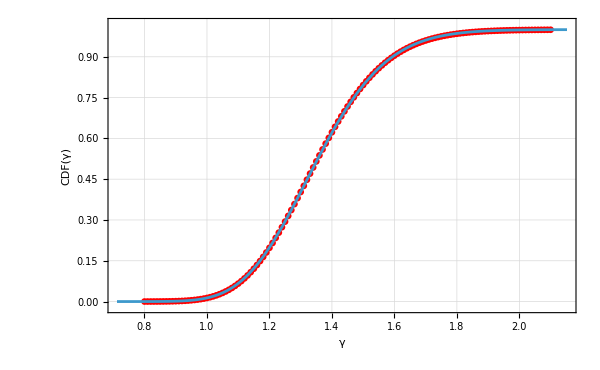

```mathematica
Plot[g[z],Prepend[{0.8,1.05}*s[[{1,-1},1]],z],
Axes->False,
Prolog->{Red,PointSize[0.008],Point[S]},
Frame->True,
FrameLabel->{"γ","CDF(γ)"},
GridLines->Automatic,
ImageSize->600,
LabelStyle->MyTS,
PlotRange->{All,{-0.02,1.02}},
PlotRangeClipping->True]
```